```mathematica
ClearAll["Global`*"]
SetDirectory[NotebookDirectory[]];SetOptions[$FrontEndSession,NotebookAutoSave->True];
NotebookSave[];
AppendTo[$Path,FileNameJoin[{$HomeDirectory,"Dropbox","EpidCRNmodels"}]];
<<EpidCRN`;
RNs={"x1"->(1+a1)*"x1",2*"x1"->"x1","x2"->(1+a2)*"x2",2*"x2"->"x2","x1"+"x2"->(1+b)*"x1"+(1+b)*"x2"};
rts={x1,x1^2,x2,x2^2,x1*x2};
Print["reactions and transitions: ",Transpose[{RNs,rts}]//MatrixForm]
cH={a1->1,a2->1,b->3};
RN=RNs/.cH;
{spe, al, be, gam, Rv, RHS, mSi, {defFormula, defTerms, defResult}}=extMat[RNs];
Print["RHS=",RHS//Factor//MatrixForm,"gam=",gam//MatrixForm];
gam.rts//MatrixForm
{RHS, var, par, cp, mSi, Jx, Jy, E0, K, R0A, infVars,al,be,gam,ng}= bdAn[RNs,rts];
Print["RHS=",RHS//Factor//MatrixForm,"gam=",gam//MatrixForm];
```

reactions and transitions: (x1→x1 (1+a1) | x1
2 x1→x1 | x1^2
x2→x2 (1+a2) | x2
2 x2→x2 | x2^2
x1+x2→x1 (1+b)+x2 (1+b) | x1 x2)

RHS=(x1 (a1 k1-k2 x1+b k5 x2)
x2 (a2 k3+b k5 x1-k4 x2))gam=(a1 | -1 | 0 | 0 | b
0 | 0 | a2 | -1 | b)

(a1 x1-x1^2+b x1 x2
a2 x2+b x1 x2-x2^2)

RHS=(x1 (a1-x1+b x2)
(a2+b x1-x2) x2)gam=(a1 | -1 | 0 | 0 | b
0 | 0 | a2 | -1 | b)

minimal siph={{{x1},{x2}},{{x1,x2}}}

autocat. sets={{{x1},{x2}},{{x1,x2}}}

Minimal siphons: {T_1→{x1},T_2→{x2}}

IGMS edges: {1→2,2→1}

Cycles found: 1

Cycles: {{1->2,2->1}}

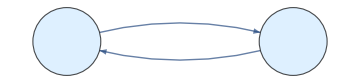

```mathematica
Print["minimal siph=",minSiph[spe,RNs]]
Print["autocat. sets=",findCores[RNs,2]]
IGMS[RNs, mSi];
```

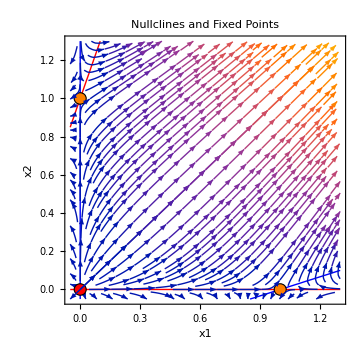

```mathematica
Show[plotFP,plotStream]
```

```mathematica
?EpidCRN`*
```